# Bicycle Equations

## Obtain bicycle equation:

```mathematica
p={x1[t], y1[t]};q={x2[t], y2[t]};
ans=1/l^2*D[p, t].(p-q)*(p-q)//Simplify
ans//Expand
```

{((x1[t]-x2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2,((y1[t]-y2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2}

{(x1[t]^2 x1'[t])/l^2-(2 x1[t] x2[t] x1'[t])/l^2+(x2[t]^2 x1'[t])/l^2+(x1[t] y1[t] y1'[t])/l^2-(x2[t] y1[t] y1'[t])/l^2-(x1[t] y2[t] y1'[t])/l^2+(x2[t] y2[t] y1'[t])/l^2,(x1[t] y1[t] x1'[t])/l^2-(x2[t] y1[t] x1'[t])/l^2-(x1[t] y2[t] x1'[t])/l^2+(x2[t] y2[t] x1'[t])/l^2+(y1[t]^2 y1'[t])/l^2-(2 y1[t] y2[t] y1'[t])/l^2+(y2[t]^2 y1'[t])/l^2}

## Cannot solve analytically.

```mathematica
eqn1=ans[[1]];
eqn2=ans[[2]];
DSolve[{x2'[t]==eqn1,y2'[t]==eqn2},{x2,y2},t]
```

DSolve[{x2'[t]==((x1[t]-x2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2,y2'[t]==((y1[t]-y2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2},{x2,y2},t]

## Straight line motion.

x1[t]=t, y1[t]=0;
Following are solutions without initial conditions.

```mathematica
line1=((x1[t]-x2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2/.{x1[t]->t,x1'[t]->1,y1[t]->0,y1'[t]->0};
line2=((y1[t]-y2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2/.{x1[t]->t,x1'[t]->1,y1[t]->0,y1'[t]->0};
linesolve=DSolve[{x2'[t]==line1,y2'[t]==line2},{x2[t],y2[t]},t];
equation11=line1/.l->1
equation12=line2/.l->1
linesim=Simplify[linesolve[[1]],t≥0&&l>0]
Collect[linesim[[1]],t]
Collect[linesim[[2]],t]
```

(t-x2[t])^2

-(t-x2[t]) y2[t]

{{x→InterpolatingFunction[{{1.,10.}},<>],y→InterpolatingFunction[{{1.,10.}},<>]}}

linesolve

1

```mathematica
2 l^2+(-l)*(l+2 ⅇ^((2 t)/l) C[1])//Simplify
```

l (l-2 c_1 ⅇ^((2 t)/l))

```mathematica
Solve[(l-c1)/(l+c1)==m,c1]
```

{{c1→(l-l m)/(1+m)}}

Obtain X2(t):

```mathematica
Simplify[l*(l-C1 ⅇ^((2 t)/l))/(C1 ⅇ^((2 t)/l)+l)+t/.C1->(l-l m)/(m+1)]
```

```mathematica
-(l (1+ⅇ^((2 t)/l) (-1+m)+m))/(-1+ⅇ^((2 t)/l) (-1+m)-m)+t/.{m->1,t->0}
```

l

Obtain Y2(t):

```mathematica
-(l (1+ⅇ^((2 t)/l) (-1+m)+m))/(-1+ⅇ^((2 t)/l) (-1+m)-m)+t/.t->s
```

-(l (1+ⅇ^((2 s)/l) (-1+m)+m))/(-1+ⅇ^((2 s)/l) (-1+m)-m)+s

```mathematica
1/l^2*∫_0^t (-(l (1+ⅇ^((2 s)/l) (-1+m)+m))/(-1+ⅇ^((2 s)/l) (-1+m)-m)+s-s)ⅆs
```

(t+l Log[2]-l Log[1-ⅇ^((2 t)/l) (-1+m)+m])/l

```mathematica
l*Sin[alpha]*Exp[(t+l Log[2]-l Log[1-ⅇ^((2 t)/l) (-1+m)+m])/l]/.m->Cos[alpha]//Simplify
```

```mathematica
(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])/.{alpha->Pi/2,t->0}
```

l

Finally, X2(t) and Y2(t):

```mathematica
-(l (1+ⅇ^((2 t)/l) (-1+m)+m))/(-1+ⅇ^((2 t)/l) (-1+m)-m)+t/.m->Cos[alpha]//Simplify
(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])//Simplify
```

t-(l (1+ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha]))/(-1+ⅇ^((2 t)/l) (-1+Cos[alpha])-Cos[alpha])

(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])

Verify results:

```mathematica
{t-(l (1+ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha]))/(-1+ⅇ^((2 t)/l) (-1+Cos[alpha])-Cos[alpha]),(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])}/.{t->0,alpha->Pi/2}
```

```mathematica
expr={t-(l (1+ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha]))/(-1+ⅇ^((2 t)/l) (-1+Cos[alpha])-Cos[alpha]),(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])}/.l->1
```

{t-(1+ⅇ^(2 t) (-1+Cos[alpha])+Cos[alpha])/(-1+ⅇ^(2 t) (-1+Cos[alpha])-Cos[alpha]),(2 ⅇ^t Sin[alpha])/(1-ⅇ^(2 t) (-1+Cos[alpha])+Cos[alpha])}

```mathematica
param1[alpha_]:=t-(1+ⅇ^(2 t) (-1+Cos[alpha])+Cos[alpha])/(-1+ⅇ^(2 t) (-1+Cos[alpha])-Cos[alpha]);
param2[alpha_]:=(2 ⅇ^t Sin[alpha])/(1-ⅇ^(2 t) (-1+Cos[alpha])+Cos[alpha]);
Table[i*Pi/6,{i,0,11}]
Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]
Show[%]
```

{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6}

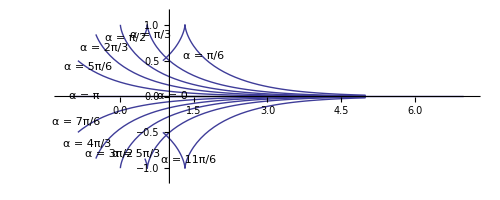

Study the critical point: y2’=0

```mathematica
D[(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha]),t]//Simplify
```

(2 ⅇ^(t/l) (1-ⅇ^((2 t)/l)+(1+ⅇ^((2 t)/l)) Cos[alpha]) Sin[alpha])/((1+ⅇ^((2 t)/l)+Cos[alpha]-ⅇ^((2 t)/l) Cos[alpha])^2)

```mathematica
y2der=(2 Sin[alpha] ⅇ^(t/l) (Cos[alpha] (ⅇ^((2 t)/l)+1)-ⅇ^((2 t)/l)+1))/((Cos[alpha] (-ⅇ^((2 t)/l))+Cos[alpha]+ⅇ^((2 t)/l)+1)^2)/.t/l->xvalue
```

(2 ⅇ^xvalue (1-ⅇ^(2 xvalue)+(1+ⅇ^(2 xvalue)) Cos[alpha]) Sin[alpha])/((1+ⅇ^(2 xvalue)+Cos[alpha]-ⅇ^(2 xvalue) Cos[alpha])^2)

```mathematica
Solve[{sim==0,xvalue>0},xvalue]
```

{{xvalue→ConditionalExpression[1/2 Log[(-1-Cos[alpha])/(-1+Cos[alpha])],0<Cos[alpha]<1]}}

```mathematica
Table[1/2 Log[(-1-Cos[alpha])/(-1+Cos[alpha])],{alpha,0,2 Pi,Pi/6}]//N
```

Power::infy: Infinite expression 1/0 encountered.

{∞,1.31696,0.549306,0.,-0.549306,-1.31696,-∞,-1.31696,-0.549306,0.,0.549306,1.31696,∞}

下面说明了上面算出的根就是y2函数的对称轴

```mathematica
y2value=(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])
y2value02=y2value/.xvalue->2*1/2 Log[(-1-Cos[alpha])/(-1+Cos[alpha])]-yvalue//Simplify
y2value/.{alpha->Pi/3,yvalue->.5}
y2value02/.{alpha->Pi/3,xvalue->.5}
```

(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])

(2 ⅇ^(t/l) l Sin[alpha])/(1-ⅇ^((2 t)/l) (-1+Cos[alpha])+Cos[alpha])

(√3 ⅇ^(t/l) l)/(3/2+1/2 ⅇ^((2 t)/l))

(√3 ⅇ^(t/l) l)/(3/2+1/2 ⅇ^((2 t)/l))

y2: Take alpha=Pi/3, l=1 as an example.

(√3 ⅇ^t)/(3/2+ⅇ^(2 t)/2)

Log[3]/2

1

(2 √3 ⅇ^bt)/(3+ⅇ^(2 bt))

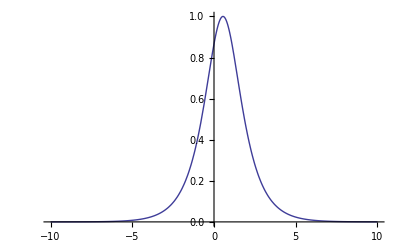

```mathematica
examp=(2 ⅇ^t Sin[alpha])/(1-ⅇ^(2 t) (-1+Cos[alpha])+Cos[alpha])/.alpha->Pi/3
exampt=1/2 Log[(-1-Cos[alpha])/(-1+Cos[alpha])]/.alpha->Pi/3
examp/.t->exampt
examp/.t->2 exampt-bt//Simplify

Plot[examp,{t,-10,10},AxesOrigin->{0,0}]
```

Study the complete motion 2Pi/3

```mathematica
g01=ParametricPlot[{param1[2*Pi/3],param2[2*Pi/3]},{t,-6,0},PlotRange->All,PlotStyle->{Dashed}];
g02=ParametricPlot[{param1[2*Pi/3],param2[2*Pi/3]},{t,0,4},PlotRange->All];
g03=ParametricPlot[{Cos[theta],Sin[theta]},{theta,0,2 Pi},PlotRange->All,PlotStyle->{Dashed,Orange}];
g04=ListPlot[{{Cos[2 Pi/3],Sin[2 Pi/3]}},PlotMarkers->Automatic];
g05=ListLinePlot[{{0,0},{Cos[2 Pi/3],Sin[2 Pi/3]}},PlotStyle->{Pink,Thick}];
g06=ListLinePlot[{{Cos[2 Pi/3],0},{Cos[2 Pi/3],Sin[2 Pi/3]}},PlotStyle->{Black,Dotted}];
Show[g01,g02,g03,g04,g05,g06,AxesOrigin->{0,0},PlotLabel->"α = 2π/3"]
```

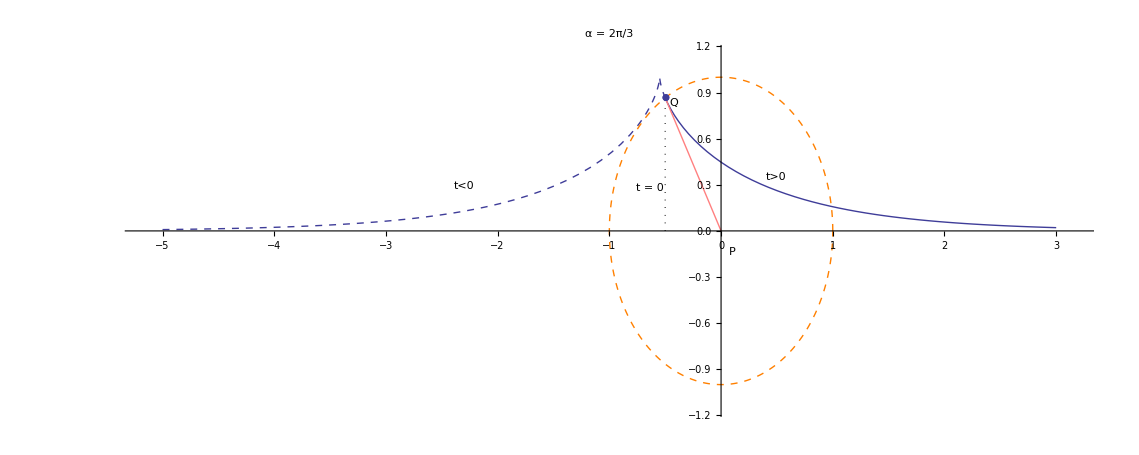

## Circular motion.

(x1,y1)=r(cos(t),sin(t))

```mathematica
ClearAll;
x1[t_]:=r Cos[t];
y1[t_]:=r Sin[t];
eq1=((x1[t]-x2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2//Expand
eq2=((y1[t]-y2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2//Expand
```

(r^2 Cos[t] Sin[t] x2[t])/l^2-(r Sin[t] x2[t]^2)/l^2-(r^2 Cos[t]^2 y2[t])/l^2+(r Cos[t] x2[t] y2[t])/l^2

(r^2 Sin[t]^2 x2[t])/l^2-(r^2 Cos[t] Sin[t] y2[t])/l^2-(r Sin[t] x2[t] y2[t])/l^2+(r Cos[t] y2[t]^2)/l^2

(Cos[t]/2-x2[t]) (-1/2 Sin[t] (Cos[t]/2-x2[t])+1/2 Cos[t] (Sin[t]/2-y2[t]))

(-1/2 Sin[t] (Cos[t]/2-x2[t])+1/2 Cos[t] (Sin[t]/2-y2[t])) (Sin[t]/2-y2[t])

{{x2→InterpolatingFunction[{{0.,3.92699}},<>],y2→InterpolatingFunction[{{0.,3.92699}},<>]}}

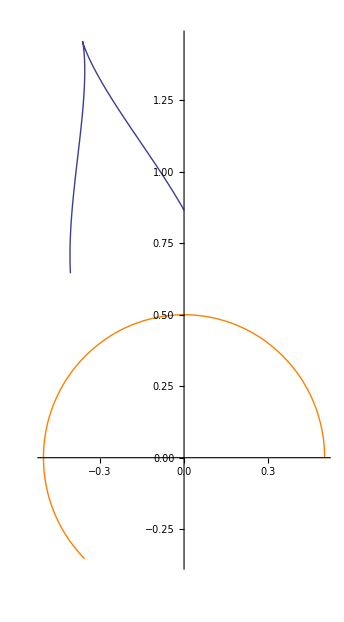

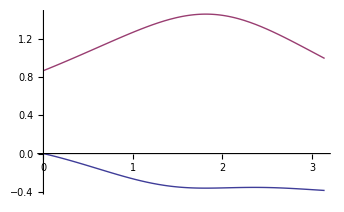

```mathematica
ClearAll;
arceqn1=((x1[t]-x2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2;
arceqn2=((y1[t]-y2[t]) ((x1[t]-x2[t]) x1'[t]+(y1[t]-y2[t]) y1'[t]))/l^2;
r0=1/2;l0=1;alpha=2/3 Pi;
x2Ini=r0+l0 Cos[alpha];
y2Ini=l0 Sin[alpha];
x1arc=r Cos[t]/.{r->r0};
y1arc=r Sin[t]/.{r->r0};
x1der=D[x1arc,t];
y1der=D[y1arc,t];
motionX=arceqn1/.{x1[t]->x1arc,x1'[t]->x1der,y1[t]->y1arc,y1'[t]->y1der,l->l0}
motionY=arceqn2/.{x1[t]->x1arc,x1'[t]->x1der,y1[t]->y1arc,y1'[t]->y1der,l->l0}
(*arcSolve=NDSolve[{x2'[t]==motionX,y2'[t]==motionY,x1[0]==1,y1[0]==0},{x2,y2},{t,0,10}]*)
s=NDSolve[{x2'[t]==motionX,y2'[t]==motionY,x2[0]==x2Ini,y2[0]==y2Ini},{x2,y2},{t,0,1.25 Pi}]
graphFront=ParametricPlot[{x1arc,y1arc},{t,0,1.25 Pi},PlotStyle->{Orange}];
graphRear=ParametricPlot[Evaluate[{x2[t],y2[t]}/.s],{t,0,1.25 Pi}];
Show[graphFront,graphRear,AxesOrigin->{0,0},PlotRange->All]
Plot[Evaluate[{x2[t],y2[t]}/.First[s]],{t,0,Pi}]
```

l<r case: l=1, When r=2 with different alpha values

```mathematica
ClearAll;
(*Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]*)
timeStart=-20 Pi;
timeEnd=20 Pi;
solu=Table[NDSolve[{x2'[t]==(2 Cos[t]-x2[t]) (-2 Sin[t] (2 Cos[t]-x2[t])+2 Cos[t] (2 Sin[t]-y2[t])),y2'[t]==(-2 Sin[t] (2 Cos[t]-x2[t])+2 Cos[t] (2 Sin[t]-y2[t])) (2 Sin[t]-y2[t]),x2[0]==2+Cos[alpha],y2[0]==Sin[alpha]},{x2,y2},{t,timeStart,timeEnd}],{alpha,0,11/6 Pi,Pi/6}];
graphF=ParametricPlot[{2Cos[t],2 Sin[t]},{t,timeStart,timeEnd},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphSolu=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,timeEnd},AxesOrigin->{0,0},PlotRange->All],{i,1,12}];
Show[graphF,graphSolu,AxesOrigin->{0,0},PlotRange->All]
graphSoluT=Table[Show[graphF,graphSolu[[i]],PlotRange->All,AxesOrigin->{0,0},PlotLabel->"α ="<>ToString[(i-1)*Pi/6,TraditionalForm]],{i,1,12}]
GraphicsGrid[{{graphSoluT[[1]],graphSoluT[[2]],graphSoluT[[3]],graphSoluT[[4]]},{graphSoluT[[5]],graphSoluT[[6]],graphSoluT[[7]],graphSoluT[[8]]},{graphSoluT[[9]],graphSoluT[[10]],graphSoluT[[11]],graphSoluT[[12]]}}]
GraphNormal=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,timeEnd},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,7,8,9,10,11,12}}];
GraphNormalExcept59=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,timeEnd},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,2,3,4,6,7,8,10,11,12}}];
GraphCircle1=ParametricPlot[{2 Cos[alpha],2 Sin[alpha]},{alpha,0,2 Pi},PlotStyle->{Orange,Dashed,Thin}];
GraphCircle2=ParametricPlot[{Sqrt[3] Cos[theta],Sqrt[3] Sin[theta]},{theta,0,2 Pi},PlotStyle->{Blue,Dashed,Thin}];
graphFThick=ParametricPlot[{2Cos[t],2 Sin[t]},{t,timeStart,timeEnd},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphUnitCircle=ParametricPlot[{2+Cos[beta],Sin[beta]},{beta,0,2 Pi},PlotStyle->{Magenta,Dotted}];
Show[GraphCircle1,GraphCircle2,graphUnitCircle,graphFThick,GraphNormal,AxesOrigin->{0,0},PlotRange->All]
collectedGraph=Show[GraphCircle1,GraphCircle2,graphUnitCircle,graphFThick,GraphNormalExcept59,AxesOrigin->{0,0},PlotRange->All]
GraphicsRow[{collectedGraph,graphSoluT[[2]],graphSoluT[[6]]}]
```

l=r case: l=r=1.

{{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}},{{x2→InterpolatingFunction[{{-62.8319,62.8319}},<>],y2→InterpolatingFunction[{{-62.8319,62.8319}},<>]}}}

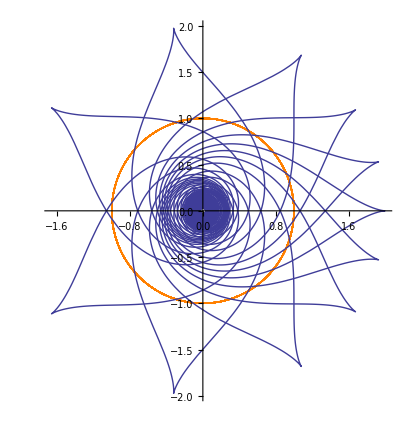

```mathematica
ClearAll;
(*Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]*)
timeStart=-20 Pi;
time=20 Pi;
solu=Table[NDSolve[{x2'[t]==(Cos[t]-x2[t]) (-Sin[t] (Cos[t]-x2[t])+Cos[t] (Sin[t]-y2[t])),y2'[t]==(-Sin[t] (Cos[t]-x2[t])+Cos[t] (Sin[t]-y2[t])) (Sin[t]-y2[t]),x2[0]==1+Cos[alpha],y2[0]==Sin[alpha]},{x2,y2},{t,timeStart,time}],{alpha,0,11/6 Pi,Pi/6}]
graphF=ParametricPlot[{Cos[t],Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphSolu=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All],{i,1,12}]
allcases=Show[graphF,graphSolu,AxesOrigin->{0,0},PlotRange->All]
graphSoluT=Table[Show[graphF,graphSolu[[i]],PlotRange->All,AxesOrigin->{0,0},PlotLabel->"α ="<>ToString[(i-1)*Pi/6,TraditionalForm]],{i,1,12}]
GraphicsGrid[{{graphSoluT[[1]],graphSoluT[[2]],graphSoluT[[3]],graphSoluT[[4]]},{graphSoluT[[5]],graphSoluT[[6]],graphSoluT[[7]],graphSoluT[[8]]},{graphSoluT[[9]],graphSoluT[[10]],graphSoluT[[11]],graphSoluT[[12]]}}]
GraphNormal=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,7,8,9,10,11,12}}];
GraphCircle1=ParametricPlot[{Cos[alpha],Sin[alpha]},{alpha,0,2 Pi},PlotStyle->{Orange,Dashed,Thin}];
graphFThick=ParametricPlot[{Cos[t],Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphUnitCircle=ParametricPlot[{1+Cos[beta],Sin[beta]},{beta,0,2 Pi},PlotStyle->{Magenta,Dotted}];
allcaseswithUnitcircle=Show[GraphCircle1,graphUnitCircle,graphFThick,allcases,AxesOrigin->{0,0},PlotRange->All]
nojackknife=Show[GraphCircle1,graphUnitCircle,graphFThick,GraphNormal,AxesOrigin->{0,0},PlotRange->All]
GraphicsRow[{allcaseswithUnitcircle,graphSoluT[[3]],graphSoluT[[11]]}]
```

l>r case: l=1, r=0.8 (*r=0.4*)

```mathematica
(0.8 Cos[t]-x2[t]) (-0.8 Sin[t] (0.8 Cos[t]-x2[t])+0.8 Cos[t] (0.8 Sin[t]-y2[t]))
(-0.8 Sin[t] (0.8 Cos[t]-x2[t])+0.8 Cos[t] (0.8 Sin[t]-y2[t])) (0.8 Sin[t]-y2[t])
```

{{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}},{{x2→InterpolatingFunction[{{-15.708,15.708}},<>],y2→InterpolatingFunction[{{-15.708,15.708}},<>]}}}

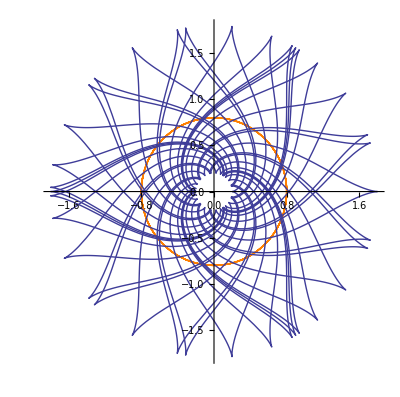

```mathematica
ClearAll;
(*Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]*)
timeStart=-5 Pi;
time=5 Pi;
solu=Table[NDSolve[{x2'[t]==(0.8  Cos[t]-x2[t]) (-0.8  Sin[t] (0.8 Cos[t]-x2[t])+0.8  Cos[t] (0.8 Sin[t]-y2[t])),y2'[t]==(-0.8 Sin[t] (0.8 Cos[t]-x2[t])+0.8 Cos[t] (0.8 Sin[t]-y2[t])) (0.8 Sin[t]-y2[t]),x2[0]==0.8+Cos[alpha],y2[0]==Sin[alpha]},{x2,y2},{t,timeStart,time}],{alpha,0,11/6 Pi,Pi/6}]
graphF=ParametricPlot[{0.8 Cos[t],0.8 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphSolu=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All],{i,1,12}]
allcases=Show[graphF,graphSolu,AxesOrigin->{0,0},PlotRange->All]
graphSoluT=Table[Show[graphF,graphSolu[[i]],PlotRange->All,AxesOrigin->{0,0},PlotLabel->"α ="<>ToString[(i-1)*Pi/6,TraditionalForm]],{i,1,12}]
GraphicsGrid[{{graphSoluT[[1]],graphSoluT[[2]],graphSoluT[[3]],graphSoluT[[4]]},{graphSoluT[[5]],graphSoluT[[6]],graphSoluT[[7]],graphSoluT[[8]]},{graphSoluT[[9]],graphSoluT[[10]],graphSoluT[[11]],graphSoluT[[12]]}}]
GraphNormal=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,7,8,9,10,11,12}}];
GraphCircle1=ParametricPlot[{0.8 Cos[alpha],0.8 Sin[alpha]},{alpha,0,2 Pi},PlotStyle->{Orange,Dashed,Thin}];
graphFThick=ParametricPlot[{0.8 Cos[t],0.8 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphUnitCircle=ParametricPlot[{0.8+Cos[beta],Sin[beta]},{beta,0,2 Pi},PlotStyle->{Magenta,Dotted}];
allcaseswithUnitcircle=Show[GraphCircle1,graphUnitCircle,graphFThick,allcases,AxesOrigin->{0,0},PlotRange->All]
nojackknife=Show[GraphCircle1,graphUnitCircle,graphFThick,GraphNormal,AxesOrigin->{0,0},PlotRange->All]
GraphicsRow[{allcaseswithUnitcircle,graphSoluT[[3]],graphSoluT[[8]]}]
```

r=0.4: Not periodic?

{{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}}}

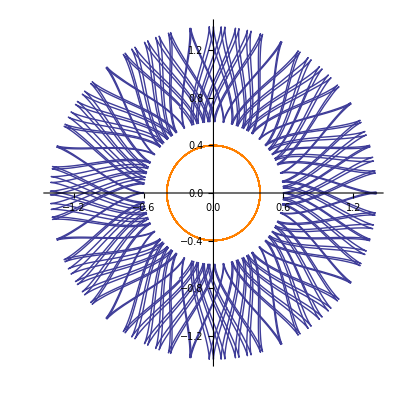

```mathematica
ClearAll;
(*Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]*)
timeStart=-12 Pi;
time=12 Pi;
solu=Table[NDSolve[{x2'[t]==((2 Cos[t])/5-x2[t]) (-2/5 Sin[t] ((2 Cos[t])/5-x2[t])+2/5 Cos[t] ((2 Sin[t])/5-y2[t])),y2'[t]==(-2/5 Sin[t] ((2 Cos[t])/5-x2[t])+2/5 Cos[t] ((2 Sin[t])/5-y2[t])) ((2 Sin[t])/5-y2[t]),x2[0]==2/5+Cos[alpha],y2[0]==Sin[alpha]},{x2,y2},{t,timeStart,time}],{alpha,0,11/6 Pi,Pi/6}]
graphF=ParametricPlot[{0.4 Cos[t],0.4 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphSolu=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All],{i,1,12}]
allcases=Show[graphF,graphSolu,AxesOrigin->{0,0},PlotRange->All]
graphSoluT=Table[Show[graphF,graphSolu[[i]],PlotRange->All,AxesOrigin->{0,0},PlotLabel->"α ="<>ToString[(i-1)*Pi/6,TraditionalForm]],{i,1,12}]
GraphicsGrid[{{graphSoluT[[1]],graphSoluT[[2]],graphSoluT[[3]],graphSoluT[[4]]},{graphSoluT[[5]],graphSoluT[[6]],graphSoluT[[7]],graphSoluT[[8]]},{graphSoluT[[9]],graphSoluT[[10]],graphSoluT[[11]],graphSoluT[[12]]}}]
GraphNormal=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,7,8,9,10,11,12}}];
GraphCircle1=ParametricPlot[{0.4 Cos[alpha],0.4 Sin[alpha]},{alpha,0,2 Pi},PlotStyle->{Orange,Dashed,Thin}];
graphFThick=ParametricPlot[{0.4 Cos[t],0.4 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphUnitCircle=ParametricPlot[{0.4+Cos[beta],Sin[beta]},{beta,0,2 Pi},PlotStyle->{Magenta,Dotted}];
allcaseswithUnitcircle=Show[GraphCircle1,graphUnitCircle,graphFThick,allcases,AxesOrigin->{0,0},PlotRange->All]
nojackknife=Show[GraphCircle1,graphUnitCircle,graphFThick,GraphNormal,AxesOrigin->{0,0},PlotRange->All]
GraphicsRow[{allcaseswithUnitcircle,graphSoluT[[3]],graphSoluT[[8]]}]
```

l=2r special case: r=0.5

{{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}},{{x2→InterpolatingFunction[{{-37.6991,37.6991}},<>],y2→InterpolatingFunction[{{-37.6991,37.6991}},<>]}}}

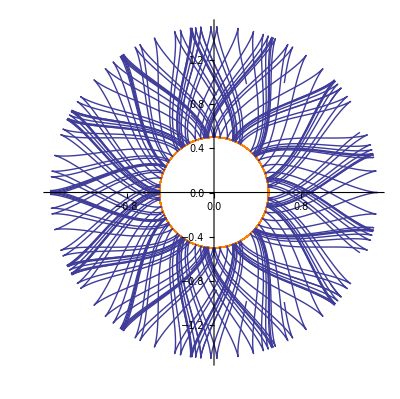

```mathematica
ClearAll;
(*Table[ParametricPlot[{param1[i*Pi/6],param2[i*Pi/6]},{t,0,6},PlotRange->All],{i,0,11}]*)
timeStart=-12 Pi;
time=12 Pi;
solu=Table[NDSolve[{x2'[t]==(Cos[t]/2-x2[t]) (-1/2 Sin[t] (Cos[t]/2-x2[t])+1/2 Cos[t] (Sin[t]/2-y2[t])),y2'[t]==(-1/2 Sin[t] (Cos[t]/2-x2[t])+1/2 Cos[t] (Sin[t]/2-y2[t])) (Sin[t]/2-y2[t]),x2[0]==1/2+Cos[alpha],y2[0]==Sin[alpha]},{x2,y2},{t,timeStart,time}],{alpha,0,11/6 Pi,Pi/6}]
graphF=ParametricPlot[{0.5 Cos[t],0.5 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphSolu=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All],{i,1,12}]
allcases=Show[graphF,graphSolu,AxesOrigin->{0,0},PlotRange->All]
graphSoluT=Table[Show[graphF,graphSolu[[i]],PlotRange->All,AxesOrigin->{0,0},PlotLabel->"α ="<>ToString[(i-1)*Pi/6,TraditionalForm]],{i,1,12}]
GraphicsGrid[{{graphSoluT[[1]],graphSoluT[[2]],graphSoluT[[3]],graphSoluT[[4]]},{graphSoluT[[5]],graphSoluT[[6]],graphSoluT[[7]],graphSoluT[[8]]},{graphSoluT[[9]],graphSoluT[[10]],graphSoluT[[11]],graphSoluT[[12]]}}]
GraphNormal=Table[ParametricPlot[Evaluate[{x2[t],y2[t]}/.solu[[i]]],{t,timeStart,time},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Blue}],{i,{1,7,8,9,10,11,12}}];
GraphCircle1=ParametricPlot[{0.5 Cos[alpha],0.5 Sin[alpha]},{alpha,0,2 Pi},PlotStyle->{Orange,Dashed,Thin}];
graphFThick=ParametricPlot[{0.5 Cos[t],0.5 Sin[t]},{t,timeStart,time},PlotStyle->{Orange},AxesOrigin->{0,0},PlotRange->All];
graphUnitCircle=ParametricPlot[{0.5+Cos[beta],Sin[beta]},{beta,0,2 Pi},PlotStyle->{Magenta,Dotted}];
allcaseswithUnitcircle=Show[GraphCircle1,graphUnitCircle,graphFThick,allcases,AxesOrigin->{0,0},PlotRange->All];
nojackknife=Show[GraphCircle1,graphUnitCircle,graphFThick,GraphNormal,AxesOrigin->{0,0},PlotRange->All];
GraphicsRow[{allcaseswithUnitcircle,graphSoluT[[3]],graphSoluT[[8]]}]
```

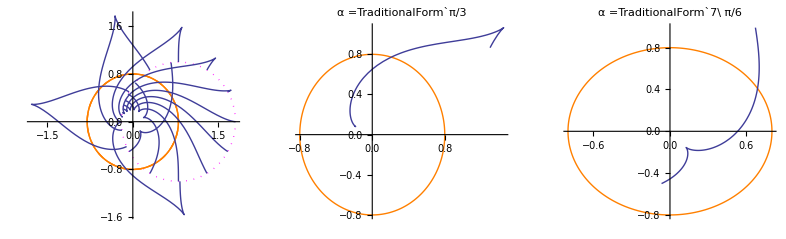
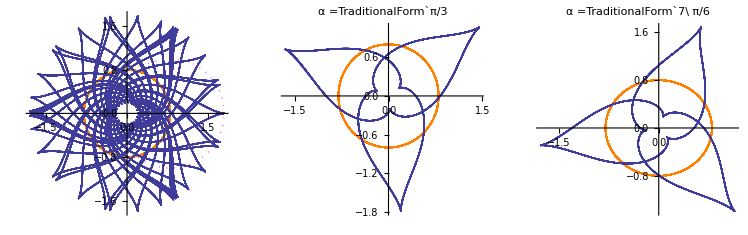
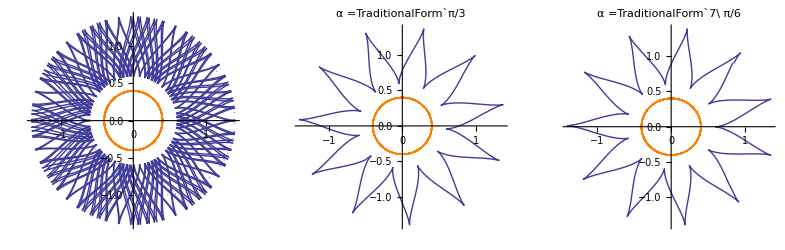
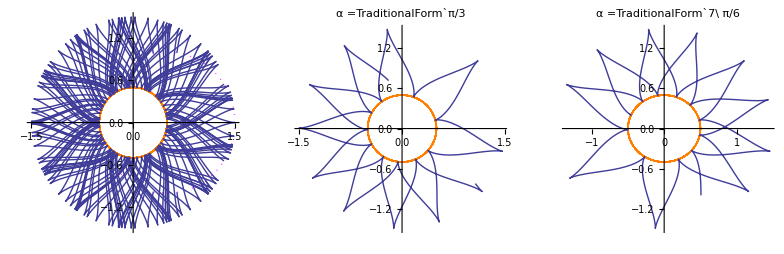
```mathematica
r08LessthanLOnePeriod=-Graphics-
r08LessthanLMultiPeriod=-Graphics-
r04Lessthan24Pi=-Graphics-
r05LessthanL24Pi=-Graphics-
```